```mathematica
SetDirectory["C:\\anaconda32\\Work\\Software\\Apps\\linacCentring\\"]
```

C:\anaconda32\Work\Software\Apps\linacCentring

```mathematica
Flatten[Table[{x,y},{x,-5,5,1},{y,-5,5,1}],1]//Length
```

121

## X Data

```mathematica
data=If[StringQ[#],ToExpression[StringReplace[#,{"["~~WhitespaceCharacter...->"{",WhitespaceCharacter...~~"]"->"}",WhitespaceCharacter..->","}]],#]&/@#&/@Rest[Import["2056 L01-SOL1_X_rawData.csv"]];
```

```mathematica
testFunc[{{a1_,b1_},{a2_,b2_}}]:=Block[{},
{If[a1<20 &&a2<20,Abs[a1-a2],20],If[b1<20 &&b2<20,Abs[b1-b2],20]}
]
```

```mathematica
plotData={#[[1]],#[[2]],Mean[testFunc[#[[{3,4}]]]]}&/@data;
```

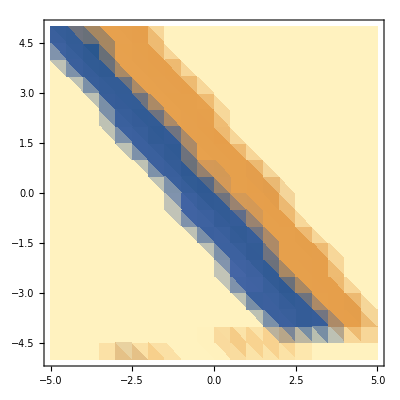

```mathematica
ListDensityPlot[plotData,Mesh->None,PlotRange->All,ColorFunctionScaling->True]
```

```mathematica
plotData[[Position[plotData,Min[plotData[[All,3]]]][[1,1]]]]
```

{-3.5,4.5,0.726925}

```mathematica
ListPlot3D[plotData,Mesh->None,InterpolationOrder->1,PlotRange->All,AxesLabel->{"C1","C2","ΔBPM"}]
```

-Graphics3D-

```mathematica
step=0.5;
UnitConvert[Length[Flatten[Table[{x,y},{x,-5,5,step},{y,-5,5,step}],1]]*Quantity[3,"Seconds"],"Minutes"]//N
```

22.05 min

## X Data 2156

```mathematica
data=If[StringQ[#],ToExpression[StringReplace[#,{"["~~WhitespaceCharacter...->"{",WhitespaceCharacter...~~"]"->"}",WhitespaceCharacter..->","}]],#]&/@#&/@Rest[Import["2156 L01-SOL1_X_rawData.csv"]];
```

```mathematica
testFunc[{{a1_},{a2_}}]:=Block[{},
If[a1<20 &&a2<20,Abs[a1-a2],20]
]
```

```mathematica
plotData={#[[1]],#[[2]],testFunc[#[[{3,4}]]]}&/@data;
```

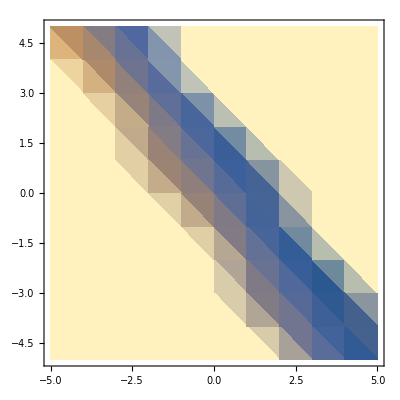

```mathematica
ListDensityPlot[plotData,Mesh->None,PlotRange->All,ColorFunctionScaling->True]
```

```mathematica
plotData[[Position[plotData,Min[plotData[[All,3]]]][[1,1]]]]
```

{3.,-2.,0.212939}

```mathematica
ListPlot3D[plotData,Mesh->None,InterpolationOrder->1,PlotRange->{All,All,{0,20}},AxesLabel->{"C1","C2","ΔBPM"}]
```

-Graphics3D-

```mathematica
step=0.5;
UnitConvert[Length[Flatten[Table[{x,y},{x,-5,5,step},{y,-5,5,step}],1]]*Quantity[3,"Seconds"],"Minutes"]//N
```

22.05 min

## Y Data 2231

```mathematica
data=If[StringQ[#],ToExpression[StringReplace[#,{"["~~WhitespaceCharacter...->"{",WhitespaceCharacter...~~"]"->"}",WhitespaceCharacter..->","}]],#]&/@#&/@Rest[Import["2231 L01-SOL1_Y_rawData.csv"]];
```

```mathematica
testFunc[{{a1_},{a2_}}]:=Block[{},
If[a1<20 &&a2<20,Abs[a1-a2],20]
]
```

```mathematica
plotData={#[[1]],#[[2]],testFunc[#[[{3,4}]]]}&/@data;
```

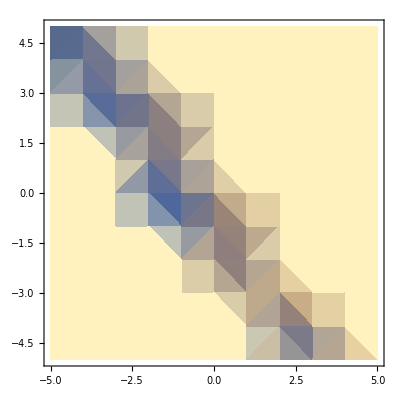

```mathematica
ListDensityPlot[plotData,Mesh->None,PlotRange->All,ColorFunctionScaling->True]
```

```mathematica
plotData[[Position[plotData,Min[plotData[[All,3]]]][[1,1]]]]
```

{-5.,4.,0.167989}

```mathematica
ListPlot3D[plotData,Mesh->None,InterpolationOrder->1,PlotRange->{All,All,{0,20}},AxesLabel->{"C1","C2","ΔBPM"}]
```

-Graphics3D-

```mathematica
step=0.5;
UnitConvert[Length[Flatten[Table[{x,y},{x,-5,5,step},{y,-5,5,step}],1]]*Quantity[3,"Seconds"],"Minutes"]//N
```

22.05 min

## X Data 2304 SOL2

```mathematica
data=If[StringQ[#],ToExpression[StringReplace[#,{"["~~WhitespaceCharacter...->"{",WhitespaceCharacter...~~"]"->"}",WhitespaceCharacter..->","}]],#]&/@#&/@Rest[Import["2304 L01-SOL2_X_rawData.csv"]];
```

```mathematica
Clear[testFunc];
testFunc[{{a1_,b1___},{a2_,b2___}}]:=Block[{},
If[a1<20 &&a2<20,Abs[a1-a2],20]
]
```

```mathematica
plotData={#[[1]],#[[2]],testFunc[#[[{3,4}]]]}&/@data;
```

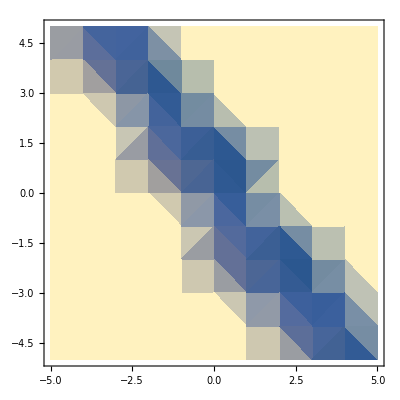

```mathematica
ListDensityPlot[plotData,Mesh->None,PlotRange->All,ColorFunctionScaling->True]
```

```mathematica
plotData[[Position[plotData,Min[plotData[[All,3]]]][[1,1]]]]
```

{0.,1.,0.0429747}

```mathematica
ListPlot3D[plotData,Mesh->None,InterpolationOrder->1,PlotRange->{All,All,{0,20}},AxesLabel->{"C1","C2","ΔBPM"}]
```

-Graphics3D-

```mathematica
step=0.5;
UnitConvert[Length[Flatten[Table[{x,y},{x,-5,5,step},{y,-5,5,step}],1]]*Quantity[3,"Seconds"],"Minutes"]//N
```

22.05 min

## Y Data 2323 SOL2

```mathematica
data=If[StringQ[#],ToExpression[StringReplace[#,{"["~~WhitespaceCharacter...->"{",WhitespaceCharacter...~~"]"->"}",WhitespaceCharacter..->","}]],#]&/@#&/@Rest[Import["2323 L01-SOL2_Y_rawData.csv"]];
```

```mathematica
Clear[testFunc];
testFunc[{{a1_,b1___},{a2_,b2___}}]:=Block[{},
If[a1<20 &&a2<20,Abs[a1-a2],20]
]
```

```mathematica
plotData={#[[1]],#[[2]],testFunc[#[[{3,4}]]]}&/@data;
```

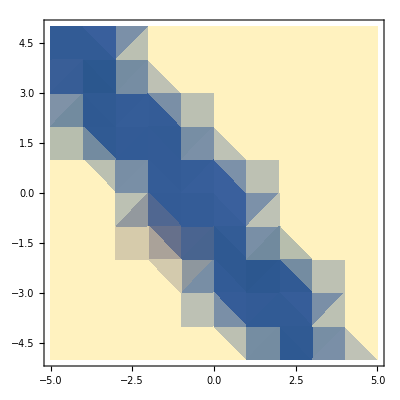

```mathematica
ListDensityPlot[plotData,Mesh->None,PlotRange->All,ColorFunctionScaling->True]
```

```mathematica
plotData[[Position[plotData,Min[plotData[[All,3]]]][[1,1]]]]
```

{2.,-2.,0.0189272}

```mathematica
ListPlot3D[plotData,Mesh->None,InterpolationOrder->1,PlotRange->{All,All,{0,20}},AxesLabel->{"C1","C2","ΔBPM"}]
```

-Graphics3D-

```mathematica
step=0.5;
UnitConvert[Length[Flatten[Table[{x,y},{x,-5,5,step},{y,-5,5,step}],1]]*Quantity[3,"Seconds"],"Minutes"]//N
```

22.05 min

## X Data 2339 SOL2

```mathematica
data=If[StringQ[#],ToExpression[StringReplace[#,{"["~~WhitespaceCharacter...->"{",WhitespaceCharacter...~~"]"->"}",WhitespaceCharacter..->","}]],#]&/@#&/@Rest[Import["2339 L01-SOL2_X_25A_50A_rawData.csv"]];
```

```mathematica
Clear[testFunc];
testFunc[{{a1_,b1___},{a2_,b2___}}]:=Block[{},
If[a1<20 &&a2<20,Abs[a1-a2],20]
]
```

```mathematica
plotData={#[[1]],#[[2]],testFunc[#[[{3,4}]]]}&/@data;
```

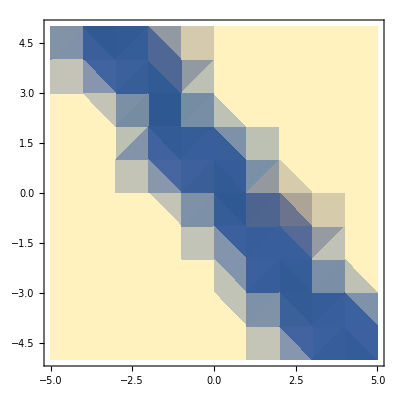

```mathematica
ListDensityPlot[plotData,Mesh->None,PlotRange->All,ColorFunctionScaling->True]
```

```mathematica
plotData[[Position[plotData,Min[plotData[[All,3]]]][[1,1]]]]
```

{4.,-5.,0.0195591}

```mathematica
ListPlot3D[plotData,Mesh->None,InterpolationOrder->1,PlotRange->{All,All,{0,20}},AxesLabel->{"C1","C2","ΔBPM"}]
```

-Graphics3D-

```mathematica
step=0.5;
UnitConvert[Length[Flatten[Table[{x,y},{x,-5,5,step},{y,-5,5,step}],1]]*Quantity[3,"Seconds"],"Minutes"]//N
```

22.05 min

## Raw Data

```mathematica
data=If[StringQ[#],ToExpression[StringReplace[#,{"["~~WhitespaceCharacter...->"{",WhitespaceCharacter...~~"]"->"}",WhitespaceCharacter..->","}]],#]&/@#&/@Rest[Import["L01-SOL1_X_rawData.csv"]];
```

```mathematica
testFunc[{{a1_},{a2_}}]:=Block[{},
If[a1<20 &&a2<20,Abs[a1-a2],20]
]
```

```mathematica
plotData={#[[1]],#[[2]],testFunc[#[[{3,4}]]]}&/@data;
```

```mathematica
ListDensityPlot[plotData,Mesh->None,PlotRange->All,ColorFunctionScaling->True]
```

-Graphics-

```mathematica
plotData[[Position[plotData,Min[plotData[[All,3]]]][[1,1]]]]
```

{3.,-2.,0.212939}

```mathematica
ListPlot3D[plotData,Mesh->None,InterpolationOrder->1,PlotRange->{All,All,{0,20}},AxesLabel->{"C1","C2","ΔBPM"}]
```

-Graphics3D-

```mathematica
step=0.5;
UnitConvert[Length[Flatten[Table[{x,y},{x,-5,5,step},{y,-5,5,step}],1]]*Quantity[3,"Seconds"],"Minutes"]//N
```

22.05 min